The Bernstein-Vazirani algorithm is a quantum algorithm that solves a specific problem known as the "oracle problem." In this problem, we are given a black-box oracle (a function) that computes a dot product between an unknown binary string "s" and an input binary string "x", modulo 2. The goal is to determine the unknown string "s".

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

Generate the Bernstein–Vazirani circuit for the secret string 101:

```mathematica
bv=QuantumCircuitOperator[{"BernsteinVazirani","101"}]
```

QuantumCircuitOperator[…]

View the circuit diagram:

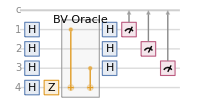

```mathematica
bv["Diagram"]
```

Show only the oracle part of the circuit:

```mathematica
QuantumCircuitOperator[{"BernsteinVaziraniOracle","101"}]["Diagram"]
```

-Graphics-

Evaluate the BV circuit and get the measurement:

```mathematica
meas=bv[]
```

QuantumMeasurement[…]

Return quantum probabilities:

```mathematica
meas["Probabilities"]
```

<|000→0,001→0,010→0,011→0,100→0,101→1,110→0,111→0|>

The only result corresponds to the secret string:

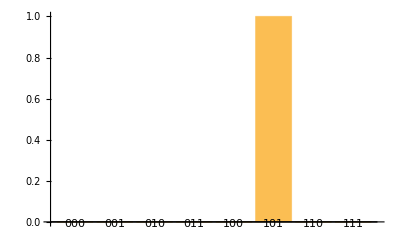

```mathematica
meas["ProbabilityPlot"]
```